```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
datax=Import["trot_0.4_allmtax.dat"];
datay=Import["trot_0.4_allmtay.dat"];
datbx=Import["trot_0.4_allmtbx.dat"];
datby=Import["trot_0.4_allmtby.dat"];
```

```mathematica
diffdata=Table[Sqrt[(Total[datax[[i]][[{1,5,9}]]])^2+(Total[datay[[i]][[{1,5,9}]]])^2],{i,1,Length[datax]}];
```

```mathematica
diffdatb=Table[Sqrt[(Total[datbx[[i]][[{1,5,9}]]])^2+(Total[datby[[i]][[{1,5,9}]]])^2],{i,1,Length[datbx]}];
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]]}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]]}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=Min[limval];
maxval=Max[limval];
```

```mathematica
squarelength=5;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

```mathematica
slcoordx1=0;
slcoordy1=2;
slcoordx2=-2;
slcoordy2=0;
slcoordx3=0;
slcoordy3=-2;
slcoordx4=2;
slcoordy4=0;
slsquareline=
{Black,Dashed,Thickness[0.015],Line[{{{slcoordx1,slcoordy1},{slcoordx2,slcoordy2}},{{slcoordx2,slcoordy2},{slcoordx3,slcoordy3}},{{slcoordx3,slcoordy3},{slcoordx4,slcoordy4}},{{slcoordx4,slcoordy4},{slcoordx1,slcoordy1}}}]};
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
ccxcoord=rmvpoints2[[All,1]];
ccycoord=rmvpoints2[[All,2]];

chxcoord=0;
chycoord=3;
sdelta=0.001;
For[i=1,i<=Length[rmvpoints2],i++,
If[chxcoord-sdelta<ccxcoord[[i]]&&ccxcoord[[i]]<chxcoord+sdelta&&chycoord-sdelta<ccycoord[[i]]&&ccycoord[[i]]<chycoord+sdelta,
point=rmvpoints2[[i]]]]
point;
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=0.3;
fsminval=0.3;
smaxval=0.65;
fsmaxval=0.65;
plrmvpoints2=Table[
If[rmvpoints2[[i,3]]<=fsminval,pt={rmvpoints2[[i,1]],rmvpoints2[[i,2]],fsminval},If[rmvpoints2[[i,3]]>=fsmaxval, pt = {rmvpoints2[[i,1]],rmvpoints2[[i,2]],fsmaxval},pt={rmvpoints2[[i,1]],rmvpoints2[[i,2]],rmvpoints2[[i,3]]}]];pt,{i,1,Length[rmvpoints2]}];
```

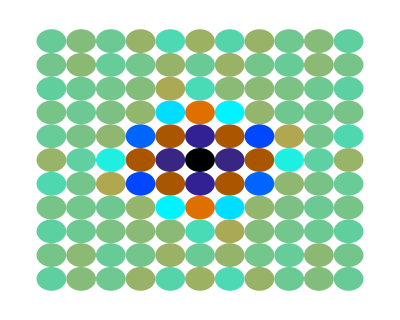

```mathematica
colorscheme={{0.3,Darker[Brown]},{0.4,Blue},{0.45,Cyan},{0.64,Orange},{0.65,Darker[Orange]}};

spointlegend=BarLegend[{(Blend[colorscheme,#]&),{fsminval,fsmaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
sqgraphicsplot = Graphics[Join[Table[{Blend[colorscheme,plrmvpoints2[[i,3]]],Rotate[Disk[{plrmvpoints2[[i,1]],plrmvpoints2[[i,2]]},{0.5,0.5}],0]},{i,1,Length[plrmvpoints2]}],{Black,Disk[{0,0},{0.5,0.5}]}],ImagePadding->{{15,12},{13,8}},ImageSize->400,AspectRatio->0.8];

finsqgraphicsplot =sqgraphicsplot 
Export["finsqgraphicsplot.eps",finsqgraphicsplot];
Export["spointlegend.png",spointlegend];
```